Acoustic Power Transmission Coefficient Equation (SI)

```mathematica
T[v_, S_,f_,Lprime_,Sb_,V_]:=((1+(((v/(2*S))/(((f*(2*Pi))*Lprime/Sb)-(v^2/((f*(2*Pi))*V)))))^2)^-1)(*Power transmission Equation (Angular freq units conversion)*)
L[f_,Lprime_,Sb_,V_]:=T[590.5,0.03810,f,Lprime,Sb,V] (*Power transmission with the values for our engine substituted*)
J[Lprime_?NumericQ,Sb_?NumericQ,V_?NumericQ]:=NIntegrate[L[f,Lprime, Sb, V],{f,350,383.333}](*Integration of the power transmission coeffiecient over the relevant range*)
B[Lprime_,Sb_, V_] := (590.5/(2*Pi))* Sqrt[Sb/(Lprime*V)](*Formula to determine resonance frequency for given variables*)
NMinimize[{J[Lprime, Sb, V], 0.0254<Lprime-(0.6*Sqrt[Sb/Pi])<0.102,0.00050670737368<Sb<0.0011399977, 0.00002895594<V<0.00193056001, B[Lprime,Sb,V]==366.6667}, {Lprime, Sb, V}, MaxIterations->500](*Minimize transmission frequency in the given range of dimensions*)
(*Length 1 to 4 in (plus 0.6 * radius end correction), diameter tube 0.5 in to 1.5 in, cavity max length 6 inches, max diameter 5 in*)
```

{6.38692,{Lprime→0.0367789,Sb→0.0010808,V→0.00193056}}

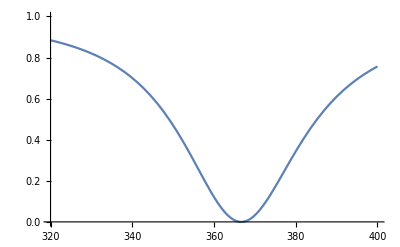

```mathematica
Plot[L[f,0.03677890041593146,0.0010807991043889757,0.0019305599647250454], {f,320,400}, PlotRange->{0,1}]
(*Current Setup*)
```